# Notebook for F_i calculations in degenerate environments

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Useful constants (run this)

Useful constants

```mathematica
mee=511;(*electron mass in keV*)
mp=1.67 10^-24;(*proton mass in grams*)
keVtoerg=1.60218 10^-9 erg/keV;(* from keV to erg*)
alpha=1/137;(* electromagnetic structure constant *)
ZO=8;(*Oxygen atomic number*)
ZC=6;(*Carbon atomic number*)
```

## Import and interpolate structure functions

Here we start to import some of the data to be used. 

We start with the data from https://www.sciencedirect.com/science/article/abs/pii/0370157387901256. In particular, we took the data from Tab.I in the Appendix (Tab.II is not useful for the parameters of interest in our work). 
Notice we added the point “ak = 0” to the tables, where the structure functions must vanish.

### Ichimaru Tables

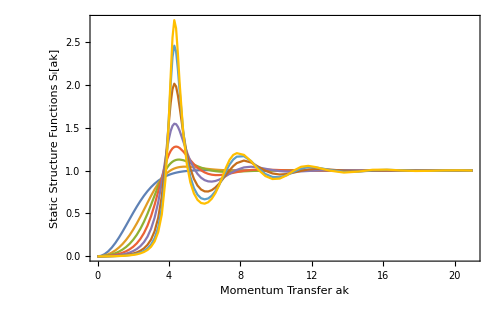

```mathematica
dat=Import[File["IchimaruTable.txt"],"Table"];
imax=Length[dat];
S2=Table[{dat[[i,1]], dat[[i,2]]},{i,1,imax}];
S5=Table[{dat[[i,1]], dat[[i,3]]},{i,1,imax}];
S10=Table[{dat[[i,1]], dat[[i,4]]},{i,1,imax}];
S20=Table[{dat[[i,1]], dat[[i,5]]},{i,1,imax}];
S40=Table[{dat[[i,1]], dat[[i,6]]},{i,1,imax}];
S80=Table[{dat[[i,1]], dat[[i,7]]},{i,1,imax}];
S125=Table[{dat[[i,1]], dat[[i,8]]},{i,1,imax}];
S160=Table[{dat[[i,1]], dat[[i,9]]},{i,1,imax}];
ListLinePlot[{S2,S5,S10,S20,S40,S80,S125,S160},Frame->True,FrameLabel->{"Momentum Transfer ak", "Static Structure Functions S_i[ak]"},ImageSize->500,FrameStyle->Directive[Black,AbsoluteThickness[0.95],15]](*Example plot*)
```

We find it useful to interpolate (in the variable “ak”) these functions.

```mathematica
Ichimaru2[ak_]:=Interpolation[S2][ak]
Ichimaru5[ak_]:=Interpolation[S5][ak]
Ichimaru10[ak_]:=Interpolation[S10][ak]
Ichimaru20[ak_]:=Interpolation[S20][ak]
Ichimaru40[ak_]:=Interpolation[S40][ak]
Ichimaru80[ak_]:=Interpolation[S80][ak]
Ichimaru125[ak_]:=Interpolation[S125][ak]
Ichimaru160[ak_]:=Interpolation[S160][ak]
```

### Itoh et al Table ApJ 273 (1983) 774-782, Table 2

Now we pass instead to consider the functions from another paper, by Itoh and collaborators. We will be using in particular the values for low Γ, which can be useful for RGs, and allow us for a better fit in a broader range of Γ.

Let’s try importing the table data

```mathematica
dataItoh=Import["AllDataItoh.dat"];(*All Data: the columns are "ak" and then all structure functions, for all values of Γ*)
```

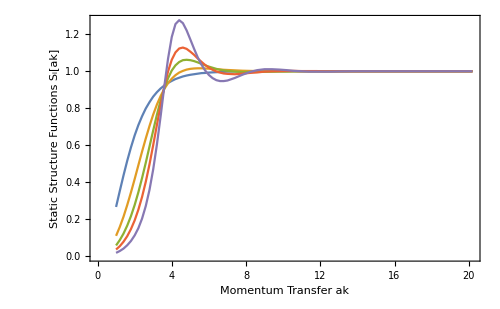

```mathematica
S1i=Table[{dataItoh[[i,1]],dataItoh[[i,2]]},{i,1,Length[dataItoh]}];
S3i=Table[{dataItoh[[i,1]],dataItoh[[i,3]]},{i,1,Length[dataItoh]}];
S6i=Table[{dataItoh[[i,1]],dataItoh[[i,4]]},{i,1,Length[dataItoh]}];
S10i=Table[{dataItoh[[i,1]],dataItoh[[i,5]]},{i,1,Length[dataItoh]}];
S20i=Table[{dataItoh[[i,1]],dataItoh[[i,6]]},{i,1,Length[dataItoh]}];
S40i=Table[{dataItoh[[i,1]],dataItoh[[i,7]]},{i,1,Length[dataItoh]}];
S80i=Table[{dataItoh[[i,1]],dataItoh[[i,8]]},{i,1,Length[dataItoh]}];
S100i=Table[{dataItoh[[i,1]],dataItoh[[i,9]]},{i,1,Length[dataItoh]}];
S125i=Table[{dataItoh[[i,1]],dataItoh[[i,10]]},{i,1,Length[dataItoh]}];
S160i=Table[{dataItoh[[i,1]],dataItoh[[i,11]]},{i,1,Length[dataItoh]}];
ListLinePlot[{S1i,S3i,S6i,S10i,S20i},Frame->True,FrameLabel->{"Momentum Transfer ak", "Static Structure Functions S_i[ak]"},ImageSize->500,FrameStyle->Directive[Black,AbsoluteThickness[0.95],15]]
```

Again we can interpolation the data we will be using

```mathematica
Itoh1High[ak_]=Interpolation[S1i][ak];
Itoh3High[ak_]=Interpolation[S3i][ak];
Itoh6High[ak_]=Interpolation[S6i][ak];
Itoh100High[ak_]=Interpolation[S100i][ak];
```

Here we also consider the small ``a k” expansion from Itoh’s paper.

```mathematica
S1small[ak_]:=Evaluate[(((3Γ)/ak^2)+0.73317-0.39890Γ+0.34141 Γ^(1/4)+0.05484 Γ^(-1/4))^-1/.Γ->1]
S3small[ak_]:=Evaluate[(((3Γ)/ak^2)+0.73317-0.39890Γ+0.34141 Γ^(1/4)+0.05484 Γ^(-1/4))^-1/.Γ->3]
S6small[ak_]:=Evaluate[(((3Γ)/ak^2)+0.73317-0.39890Γ+0.34141 Γ^(1/4)+0.05484 Γ^(-1/4))^-1/.Γ->6]
S100small[ak_]:=Evaluate[(((3Γ)/ak^2)+0.73317-0.39890Γ+0.34141 Γ^(1/4)+0.05484 Γ^(-1/4))^-1/.Γ->100]
Itoh1[ak_]:=Piecewise[{{S1small[ak],ak<1}},Itoh1High[ak]]
Itoh3[ak_]:=Piecewise[{{S3small[ak],ak<1}},Itoh3High[ak]]
Itoh6[ak_]:=Piecewise[{{S6small[ak],ak<1}},Itoh6High[ak]]
Itoh100[ak_]:=Piecewise[{{S100small[ak],ak<1}},Itoh100High[ak]]
```

## Fitting functions

Let’s now create an array for the various Γ and associated (interpolated) structure functions

```mathematica
ΓTotal={1,2,3,5,6,10,20,40,80,100,125,160}
FunctionList={Itoh1,Ichimaru2,Itoh3,Ichimaru5,Itoh6,Ichimaru10,Ichimaru20,Ichimaru40,Ichimaru80,Itoh100,Ichimaru125,Ichimaru160}
```

{1,2,3,5,6,10,20,40,80,100,125,160}

{Itoh1,Ichimaru2,Itoh3,Ichimaru5,Itoh6,Ichimaru10,Ichimaru20,Ichimaru40,Ichimaru80,Itoh100,Ichimaru125,Ichimaru160}

We now proceed to do the fit for the various cases. Every function F_i[β_F] is written as follows

F_i[β_F]=(∫_-1)^1 dx_12*(S(x_12))/(1-x_12)G_i(x_12,β_F)

which is Eq. 3.20 of our draft. We then need to specify the various G_i case by case and do the integrals.

### Axion

We start with the axion. We first of all define the following quantities:

1) ion-sphere radius a_i=((3 Z m_u)/(2π ρ))^(1/3)
2) Γ=(Z^2 α)/(a_i T)
3) Thomas-Fermi momentum for the electrons k_TF=((4α)/π E_F k_F)^(1/2)

```mathematica
ai[ρ_,A_]=((3A mp)/(4π ρ))^(1/3)cm/.cm->1/(1.97 10^-8 keV)/.keV->1;(*Pass the density in g/cm^3*)
GammaFun[Z_,ρ_,T_]=(Z^2 alpha)/(ai[ρ,2Z]T)(*pass T in keV, ρ again in g/cm^3*);
pFDegenerate[ρ_]=((3 π^2 ρ g/cm^3)/(2 mp g))^(1/3)/.cm->1/(1.97 10^-5 10^-3 keV)/.keV->1;(*Fermi momentum for a degenerate gas. Pass the density in g/cm^3, the result will be in keV*)
kElectron[ρ_]:=Block[{pF=pFDegenerate[ρ]},Sqrt[(4alpha)/π*pF Sqrt[pF^2+mee^2]]](*Pass ρ in g/cm^3. The result will be in keV*)
```

Now we can write the G_axion and then perform the integral. The variable “index” is the index of the Γ list for the interpolated function for which we had data.

```mathematica
GaxionAnalytic[x12_,β_]=3/2(1-β^2)((β-ArcTanh[β])/β^3+ArcTanh[(β Sqrt[2(1-x12)-β^2(1-x12^2)])/(1-β^2 x12)]/(β Sqrt[2(1-x12)-β^2(1-x12^2)]));
FAxionprotonNewScreeningAn[ρ_?NumericQ,Z_?NumericQ,index_?NumericQ]:=Block[{pF=pFDegenerate[ρ],βF=pF/Sqrt[pF^2+mee^2],kStrucutre=ai[ρ,2Z]pF Sqrt[2(1-x12)],kEl=kElectron[ρ],StructureF=FunctionList[[index]],x2=Sqrt[1-x1^2]Sqrt[1-x12^2]Cos[ϕ]+x1 x12},NIntegrate[GaxionAnalytic[x12,βF]*1/(1-x12)*(1-x12)^2/((1-x12+kEl^2/(2 pF^2))^2)*StructureF[kStrucutre],{x12,-1,1}]]
```

Recall that

```mathematica
ΓTotal
```

{1,2,3,5,6,10,20,40,80,100,125,160}

Give it a try for the eight place in the list, namely Γ = 40

```mathematica
FAxionprotonNewScreeningAn[10^6,ZC,8]
```

1.58625

One can then build a table for all the Γ’s for which we had data

```mathematica
TabellaToFitAxion[ρ_,Z_]:=Table[{ΓTotal[[i]],FAxionprotonNewScreeningAn[ρ,Z,i]},{i,1,Length[ΓTotal]}]
```

And we then define the fitting function which does a very good job (Eq. D.22 of our work)

```mathematica
fitParametersAxion[ρ_,Z_]:=FindFit[TabellaToFitAxion[ρ,Z],A x^-0.37+B x^0.03,{A,B},x]
```

Now we pass to fit the A and B coefficients

### Fit for Z_C

```mathematica
toUseC=Table[{ρ,fitParametersAxion[10^ρ,ZC]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρAC=Table[{toUseC[[i,1]],A/.toUseC[[i,2]]},{i,1,Length[toUseC]}];
tableρBC=Table[{toUseC[[i,1]],B/.toUseC[[i,2]]},{i,1,Length[toUseC]}];
```

```mathematica
ρAfitAxionC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρAC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitAxionC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.248497+0.392946/(8-x)^2-1.14471/(8-x)+0.306342 x

1.29252+1.1997/(8-x)^2-2.91771/(8-x)+0.152553 x

Let’s also do a numerical check for typical WD density

```mathematica
ρTry1=10^4;
ρTry2=10^5;
ρTry3=10^6;
ρTry4=10^7;

Tabella1=TabellaToFitAxion[ρTry1,ZC];(*Full numerical integrals*)
Tabella2=TabellaToFitAxion[ρTry2,ZC];(*Full numerical integrals*)
Tabella3=TabellaToFitAxion[ρTry3,ZC];(*Full numerical integrals*)
Tabella4=TabellaToFitAxion[ρTry4,ZC];(*Full numerical integrals*)


Tabella1Fit=Block[{x=Log10[ρTry1]},Table[{ΓTotal[[i]],ρAfitAxionC[x] ΓTotal[[i]]^-0.37+ρBfitAxionC[x] ΓTotal[[i]]^0.03},{i,1,Length[ΓTotal]}]];
Tabella2Fit=Block[{x=Log10[ρTry2]},Table[{ΓTotal[[i]],ρAfitAxionC[x] ΓTotal[[i]]^-0.37+ρBfitAxionC[x] ΓTotal[[i]]^0.03},{i,1,Length[ΓTotal]}]];
Tabella3Fit=Block[{x=Log10[ρTry3]},Table[{ΓTotal[[i]],ρAfitAxionC[x] ΓTotal[[i]]^-0.37+ρBfitAxionC[x] ΓTotal[[i]]^0.03},{i,1,Length[ΓTotal]}]];
Tabella4Fit=Block[{x=Log10[ρTry4]},Table[{ΓTotal[[i]],ρAfitAxionC[x] ΓTotal[[i]]^-0.37+ρBfitAxionC[x] ΓTotal[[i]]^0.03},{i,1,Length[ΓTotal]}]];
```

Plot the ratio between the numerical results and our fitting formulas

```mathematica
Ratio1=Table[{Tabella1[[i,1]],Tabella1[[i,2]]/Tabella1Fit[[i,2]]},{i,1,Length[Tabella1]}];
Ratio2=Table[{Tabella2[[i,1]],Tabella2[[i,2]]/Tabella2Fit[[i,2]]},{i,1,Length[Tabella2]}];
Ratio3=Table[{Tabella3[[i,1]],Tabella3[[i,2]]/Tabella3Fit[[i,2]]},{i,1,Length[Tabella3]}];
Ratio4=Table[{Tabella4[[i,1]],Tabella4[[i,2]]/Tabella4Fit[[i,2]]},{i,1,Length[Tabella4]}];
```

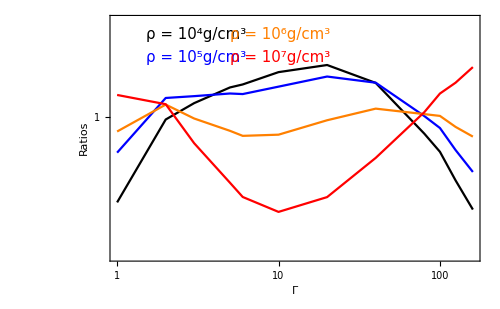

```mathematica
Show[ListLogLogPlot[{Ratio1,Ratio2,Ratio3,Ratio4},PlotStyle->{Black,Blue,Orange,Red},Joined->True,Frame->True,FrameLabel->{"Γ", "Ratios"},ImageSize->500,FrameStyle->Directive[Black,AbsoluteThickness[0.95],15],PlotRange->{{1,160},{0.97,1.02125}}],Graphics[Inset[Rotate[Style["ρ = 10^4g/cm^3",FontSize-> 15.,Black],0.],{Log[1.5],Log[1.018]},Left]],Graphics[Inset[Rotate[Style["ρ = 10^5g/cm^3",FontSize-> 15.,Blue],0.],{Log[1.5],Log[1.013]},Left]],Graphics[Inset[Rotate[Style["ρ = 10^6g/cm^3",FontSize-> 15.,Orange],0.],{Log[5.],Log[1.018]},Left]],Graphics[Inset[Rotate[Style["ρ = 10^7g/cm^3",FontSize-> 15.,Red],0.],{Log[5.],Log[1.013]},Left]]]
```

We see that, especially for the ranges of interest (that is to say ρ≈10^6 g/cm^3 and Γ≃40-50), the precision is at the % level or even better.

### Fit for Z_O

```mathematica
toUseO=Table[{ρ,fitParametersAxion[10^ρ,ZO]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρAO=Table[{toUseO[[i,1]],A/.toUseO[[i,2]]},{i,1,Length[toUseO]}];
tableρBO=Table[{toUseO[[i,1]],B/.toUseO[[i,2]]},{i,1,Length[toUseO]}];
```

```mathematica
ρAfitAxionO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρAO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitAxionO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.133166+0.410855/(8-x)^2-1.15495/(8-x)+0.324744 x

1.40109+1.21282/(8-x)^2-3.00606/(8-x)+0.16868 x

### Scalar baryophilic

```mathematica
FprotonNewScreening[ρ_?NumericQ,Z_?NumericQ,index_?NumericQ]:=Block[{pF=pFDegenerate[ρ],βF=pF/Sqrt[pF^2+mee^2],kStrucutre=ai[ρ,2Z]pF Sqrt[2(1-x12)],kEl=kElectron[ρ],StructureF=FunctionList[[index]]},1/(2(1-βF^2))NIntegrate[(2-βF^2(1-x12))/((1-x12+kEl^2/(2 pF^2))^2)(1-x12)*StructureF[kStrucutre],{x12,-1,1}]]
```

Again we build a table for all the Γ’s for which we have data

```mathematica
TabellaToFitBaryo[ρ_,Z_]:=Table[{ΓTotal[[i]],FprotonNewScreening[ρ,Z,i]},{i,1,Length[ΓTotal]}]
```

And we then define the fitting function which does a very good job (Eq. D.22 of our work)

```mathematica
fitParametersBaryo[ρ_,Z_]:=FindFit[TabellaToFitBaryo[ρ,Z],A x^-0.37+B x^0.03,{A,B},x]
```

### Fit for Z_C

```mathematica
toUseBaryoC=Table[{ρ,fitParametersBaryo[10^ρ,ZC]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρBaryoAC=Table[{toUseBaryoC[[i,1]],A/.toUseBaryoC[[i,2]]},{i,1,Length[toUseBaryoC]}];
tableρBaryoBC=Table[{toUseBaryoC[[i,1]],B/.toUseBaryoC[[i,2]]},{i,1,Length[toUseBaryoC]}];
```

```mathematica
ρAfitBaryoC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBaryoAC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitBaryoC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBaryoBC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.665252+0.7125/(8-x)^2+6.17372/(8-x)-0.244222 x

1.34539+0.0567348/(8-x)^2+3.00022/(8-x)-0.201325 x

### Fit for Z_O

```mathematica
toUseBaryoO=Table[{ρ,fitParametersBaryo[10^ρ,ZO]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρBaryoAO=Table[{toUseBaryoO[[i,1]],A/.toUseBaryoO[[i,2]]},{i,1,Length[toUseBaryoO]}];
tableρBaryoBO=Table[{toUseBaryoO[[i,1]],B/.toUseBaryoO[[i,2]]},{i,1,Length[toUseBaryoO]}];
```

```mathematica
ρAfitBaryoO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBaryoAO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitBaryoO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρBaryoBO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.560391+0.749343/(8-x)^2+6.16094/(8-x)-0.228741 x

1.49243+0.0960619/(8-x)^2+3.65998/(8-x)-0.240196 x

### Scalar leptophilic

```mathematica
GLeptonAnalytic[x_,β_]=-3/2+3/(β^2(1-x))-(3(1-β^2)(2-β^2(1-x)))/(4 β^3(1-x)^(5/2)(2-β^2(1+x))^(3/2))((2-x)ArcTanh[(β Sqrt[(1-x)(2-β^2(1+x))])/(1-β^2 x)]+(1-β^2(1-x^2)-3x/2)ArcTanh[(2β(1-β^2 x) Sqrt[(1-x)(2-β^2(1+x))])/(1+2 β^2(1-2x)-β^4(1-2 x^2))]);
```

```mathematica
FLeptonNewScreeningAn[ρ_?NumericQ,Z_?NumericQ,index_?NumericQ]:=Block[{pF=pFDegenerate[ρ],βF=pF/Sqrt[pF^2+mee^2],kStrucutre=ai[ρ,2Z]pF Sqrt[2(1-x12)],kEl=kElectron[ρ],StructureF=FunctionList[[index]],x2=Sqrt[1-x1^2]Sqrt[1-x12^2]Cos[ϕ]+x1 x12},NIntegrate[GLeptonAnalytic[x12,βF]*1/(1-x12)*(1-x12)^2/((1-x12+kEl^2/(2 pF^2))^2)*StructureF[kStrucutre],{x12,-1,1}]]
```

Again we build a table for all the Γ’s for which we have data

```mathematica
TabellaToFitLepto[ρ_,Z_]:=Table[{ΓTotal[[i]],FLeptonNewScreeningAn[ρ,Z,i]},{i,1,Length[ΓTotal]}]
```

And we then define the fitting function which does a very good job (Eq. D.22 of our work)

```mathematica
fitParametersLepto[ρ_,Z_]:=FindFit[TabellaToFitLepto[ρ,Z],A x^-0.37+B x^0.03,{A,B},x]
```

### Fit for Z_C

```mathematica
toUseLeptoC=Table[{ρ,fitParametersLepto[10^ρ,ZC]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρLeptoAC=Table[{toUseLeptoC[[i,1]],A/.toUseLeptoC[[i,2]]},{i,1,Length[toUseLeptoC]}];
tableρLeptoBC=Table[{toUseLeptoC[[i,1]],B/.toUseLeptoC[[i,2]]},{i,1,Length[toUseLeptoC]}];
```

```mathematica
ρAfitLeptoC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρLeptoAC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitLeptoC[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρLeptoBC,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.566616-0.542645/(8-x)^2+6.4126/(8-x)-0.21696 x

1.21381-0.231104/(8-x)^2+0.327525/(8-x)-0.00385162 x

### Fit for Z_O

```mathematica
toUseLeptoO=Table[{ρ,fitParametersLepto[10^ρ,ZO]},{ρ,4,7,0.1}];(*Fitting parameters for various densities*)
```

```mathematica
tableρLeptoAO=Table[{toUseLeptoO[[i,1]],A/.toUseLeptoO[[i,2]]},{i,1,Length[toUseLeptoO]}];
tableρLeptoBO=Table[{toUseLeptoO[[i,1]],B/.toUseLeptoO[[i,2]]},{i,1,Length[toUseLeptoO]}];
```

```mathematica
ρAfitLeptoO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρLeptoAO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
ρBfitLeptoO[x_]=a0+a x+b /(8-x)+c /(8-x)^2/.FindFit[tableρLeptoBO,a0+a x+b /(8-x)+c /(8-x)^2,{a0,a,b,c},x]
```

0.468476-0.367875/(8-x)^2+6.30468/(8-x)-0.199265 x

1.33835-0.452269/(8-x)^2+1.09373/(8-x)-0.0400191 x